# Efeito das Aproximações no Cálculo de Parâmetros para Cabos SC

## Antonio Carlos Siqueira de Lima Departamento de Engenharia Elétrica Universidade Federal do Rio de Janeiro acsl@dee.ufrj.br

## Opções de Projeto

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Frame->True,Axes->True,ImageSize->450,Joined->True,PlotStyle->{Thick}];
```

```mathematica
plstyle1={AbsoluteThickness[2],RGBColor[1,0,0], Hue[0]};
plstyle2={AbsoluteThickness[2],AbsoluteDashing[{5,0,5}],RGBColor[0,0,1]};
plstyle3={AbsoluteThickness[2],PointSize[.015],RGBColor[1,0,1]};
plstyle4={AbsoluteThickness[2],PointSize[.015],RGBColor[0,0,0]};
```

## Dados de entrada

Dimensões dos cabos

```mathematica
r1=1 10^-2;
r2=1.2 10^-2;
```

Constantes Elétricas e Parâmetros do Solo por metro

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12; 
ϵcs=3;
ϵg=10;
ϵ1=ϵcs ϵ;
ρc=3.365 10^-8;
ρ=20;
ηc=√((ⅉ  ω μ)/ρc);
σ=1/ρ;
(*w=(σ+(0.057849+ⅉ 0.12097)10^(-6) ω^0.71603);*)
w=σ+I ω ϵ ϵg;
k2=ω √(μ ϵ);
k1=√(ω^2 μ ϵ ϵg+I ω μ σ);
γg=Sqrt[I ω μ  (σ+I ω ϵ ϵg)];
η=I k1;
```

```mathematica
ℓ=10000;
h=2 r2
```

0.024

## Desenho da rede

Espaçamento dos condutores com configuração plana

```mathematica
x1=0;x3=6 r2;x5=2 x3;
xc={x1,x1,x3,x3,x5,x5};
hc=Table[h,{i,1,Length[xc]}];
r={r1,r2,r1,r2,r1,r2};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],-hc[[i]]},r[[i]]]},{i,1,Length[xc]}];
```

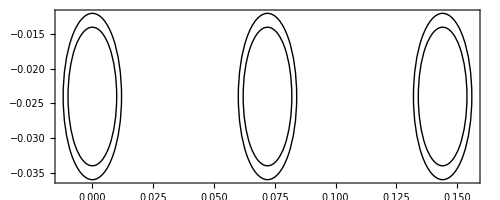

```mathematica
rr=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->True,PlotRange->All]
```

```mathematica
de=√(r2^2+4 hc[[1]]^2);
d13=√((x1-x3)^2+(hc[[1]]-hc[[3]])^2);
Dc13=√((x1-x3)^2+(hc[[1]]+hc[[3]])^2);
d15=√((x1-x5)^2+(hc[[1]]-hc[[5]])^2);
Dc15=√((x1-x5)^2+(hc[[1]]+hc[[5]])^2);
```

## Frequências e listas

#### Faixa de Frequência

```mathematica
logspace[f1_,f2_,n_]:=Table[10^(f1+((f2-f1)/(n-1))*x),{x,0,n-1}]//N;
f=logspace[-2,8,120];
nf=Dimensions[f][[1]];
```

```mathematica
Max[f]
```

1.×10^8

Inicializando listas para o fator de propagação e para admitância característica

```mathematica
Yn=Table[0,{n,1,nf}];
eigAfase=Yn;
eigAfase2=Yn;
Yn2=Yn;
eigAfase3=Yn;
Yn3=Yn;
Zcabo=Yn;
Ycabo=Yn;
Ycabo2=Yn;
Ycabo3=Yn;
Ycabo4=Yn;
d=Yn;
```

## Cálculo usando as formulação de Bessel & Pollaczek

```mathematica
Timing[Do[{ω=2π f[[nm]],
(* Impedancias internas*)
z1=(ρc ηc)/(2π r1)BesselI[0,ηc r1]/BesselI[1,ηc r1],
z2=ⅉ(ω μ)/(2π)Log[r2/r1],
(* Impedancias externas*)
int=10,
Js=2 NIntegrate[Exp[-2 hc[[1]] √(α^2+η^2)]/(Abs[α]+√(α^2+η^2))Cos[r2 α],{α,0,int},MaxRecursion->50],
Jm13=2 NIntegrate[Exp[-(hc[[1]]+hc[[3]]) √(α^2+η^2)]/(Abs[α]+√(α^2+η^2))Cos[(x3-x1) α],{α,0,int},MaxRecursion->50],
Jm15=2 NIntegrate[Exp[-(hc[[1]]+hc[[5]]) √(α^2+η^2)]/(Abs[α]+√(α^2+η^2))Cos[(x3-x1) α],{α,0,int},MaxRecursion->50],
z7=(ρ η^2)/(2 π)(BesselK[0,η r2]-BesselK[0,η de ]+Js),
(*z7=(ⅈ ω μ)/(2π)(BesselK[0,r2 η]+((4hc[[1]]^2-r2^2)  BesselK[2,η  de])/de^2-2 (4hc[[1]]^2-r2^2) Exp[-2hc[[1]] η]/(η^2 ( de^4))( 1+2hc[[1]] η )),,*)
(*z7=ⅉ(ω μ)/(2π)(-Log[(EulerGamma η r2)/2]+1/2-(4η)/3 hc[[1]]),*)
Zm1solo=(ρ η^2)/(2 π)(BesselK[0,η (x3-x1)]-BesselK[0,η Dc13]+Jm13),
Zm2solo=(ρ η^2)/(2 π)(BesselK[0,η (x5-x1)]-BesselK[0,η Dc15]+Jm15),
Zint={{z1+z2+z7}},
Zcabo[[nm]]=ArrayFlatten[{{Zint,Zm1solo,Zm2solo},{Zm1solo,Zint,Zm1solo},{Zm2solo,Zm1solo,Zint}}],

(*MODELO DE ADMITÂNCIA N° 01 - Modelo proposto*)
(* matrix de admitância externa*)
pc=Log[r2/r1]/(2 π ϵ1) ,
d[[nm]]=((k2^2)/(k1^2))  η,
si[k_]:=-π/2+NIntegrate[Sin[t]/t,{t,0,k}],
ci[k_]:=(*C+*)Log[k]+NIntegrate[(Cos[t]-1)/t,{t,0,k}],
Jy3[a_,β_]:=Exp[-2 hc[[1]]  η](-Sin[a β] si[a β]-Cos[a β] ci[a β]),
(*Jy3=NIntegrate[Exp[-2 hc[[1]] Sqrt[ η^2]]/(Abs[α]+ ((k2^2)/(k1^2))  Sqrt[ η^2])Cos[r2 α],{α,0,int},MaxRecursion->500],*)
(*Jym1=NIntegrate[(Exp[-(hc[[1]]+hc[[3]])η)/(Abs[α]+ ((k2^2)/(k1^2)) η)Cos[(x3-x1) α],{α,0,int},MaxRecursion->500],*)
(*Jym2=NIntegrate[(Exp[-(hc[[1]]+hc[[5]])η)/(Abs[α]+ ((k2^2)/(k1^2))η)Cos[(x5-x1) α],{α,0,int},MaxRecursion->500],*)
λp3=BesselK[0,η r2]-BesselK[0,η de],
ps=(I ω)/(2 π (σ+I ω ϵ ϵg))(λp3+2 Jy3[r2,d[[nm]]]) ,
Jym1[a_,β_]:=Exp[-(hc[[1]]+hc[[3]]) η](-Sin[a β] si[a β]-Cos[a β] ci[a β]),
Jym2[a_,β_]:=Exp[-(hc[[1]]+hc[[5]]) η](-Sin[a β] si[a β]-Cos[a β] ci[a β]),

λm1=BesselK[0,η (x3-x1)]-BesselK[0,η Dc13],
λm2=BesselK[0,η (x5-x1)]-BesselK[0,η Dc15],
pm1=(I ω)/(2 π (σ+I ω ϵ ϵg))(λm1+2 Jym1[(x3-x1),d[[nm]]]),
pm2=(I ω)/(2 π (σ+I ω ϵ ϵg))(λm2+2 Jym2[(x5-x1),d[[nm]]]),
pint0={{pc,0,0},{0,pc,0},{0,0,pc}},
pext0={{ps,pm1,pm2},{pm1,ps,pm1},{pm2,pm1,ps}},
Ycabo[[nm]]=I ω Inverse[pint0+pext0],

(*MODELO DE ADMITÂNCIA N° 02 - Modelo usual*)
(* matrix de admitância interna*)
Yint=I ω / pc,
Ycabo2[[nm]]=ArrayFlatten[{{Yint,0,0},{0,Yint,0},{0,0,Yint}}],


(*MODELO DE ADMITÂNCIA N° 03 - Petrache*)
(*z72=(ⅉ ω μ)/(2 π) Log[(1+γg r2)/(γg r2)],
Yg11=(γg^2)/z72(*Zpetr*),
cpc=(2 π ϵ1)/Log[r2/r1] ,
σi=10^-20,
gdg=σi/ϵ1 cpc,
yc2=gdg+I ω cpc,
Yintext=((yc2 Yg11)/(yc2+ Yg11)),
Ygm1=(γg^2)/Zm1solo,
Ygm2=(γg^2)/Zm2solo,
Ycabo3[[nm]]={{Yintext,Ygm1,Ygm2},{Ygm1,Yintext,Ygm1},{Ygm2,Ygm1,Yintext}}*)
z72=(ⅉ ω μ)/(2 π) Log[(1+γg r2)/(γg r2)],
pg11=(I ω)/(γg^2)z72,
ppc=Log[r2/r1]/(2 π ϵ1) ,
pintext=pg11+ppc,
pgm1=(I ω)/(γg^2)((ⅉ ω μ)/(2 π) Log[(1+γg (x3-x1))/(γg (x3-x1))]),
pgm2=(I ω)/(γg^2)((ⅉ ω μ)/(2 π) Log[(1+γg (x5-x1))/(γg (x5-x1))]),
Ycabo3[[nm]]=I ω Inverse[{{pintext,pgm1,pgm2},{pgm1,pintext,pgm1},{pgm2,pgm1,pintext}}]


},{nm,1,nf}];]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.0527909937718585`*^-8 + 1.0528321957937136`*^-8 ⅈ}. NIntegrate obtained -3.809346407400412`*^-17 - 1.1025009044742942`*^-16 ⅈ and 1.98489×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.0506466124133942`*^-8 + 1.0506965087268388`*^-8 ⅈ}. NIntegrate obtained -3.835533734343362`*^-17 - 1.970061547975289`*^-16 ⅈ and 2.1991×10^-20 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.0545781351168912`*^-8 + 1.0546389103134777`*^-8 ⅈ}. NIntegrate obtained -2.5560795033132585`*^-17 - 8.80076942733687`*^-17 ⅈ and 1.77296×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{14.609,Null}

```mathematica
teste=Max[Abs[Arg[d]]]
```

1.20473

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.172,Null}

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo2[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo2[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase2[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn2[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.343,Null}

```mathematica
Timing[Do[{ω=2π f[[nm]],
eval=Eigenvalues[N[Zcabo[[nm]].Ycabo3[[nm]]]],
evect=Eigenvectors[N[Zcabo[[nm]].Ycabo3[[nm]]]],
γ=Sqrt[eval],
Tv=Transpose[evect],
Tvi=Inverse[Transpose[evect]],
hm=Exp[-γ*ℓ],
eigAfase3[[nm]]=hm,
den=(1-hm^2),
Am=γ*(1+hm^2)/den,
Bm=-2.0*γ*hm/den,
A=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Am].Tvi,
B=N[Inverse[Zcabo[[nm]]]].Tv.DiagonalMatrix[Bm].Tvi,
Ynodal=ArrayFlatten[{{A,B},{B,A}}],
Yn3[[nm]]=Eigenvalues[Ynodal]
},{nm,1,nf}];]
```

{0.219,Null}

## Conferindo

```mathematica
Ycabo[[120]]//MatrixForm
Ycabo2[[120]]//MatrixForm
Ycabo3[[120]]//MatrixForm
```

(0.0179703+0.0484824 ⅈ | -0.0106145-0.0218749 ⅈ | -0.00515582-0.00860091 ⅈ
-0.0106145-0.0218749 ⅈ | 0.0226428+0.0567827 ⅈ | -0.0106145-0.0218749 ⅈ
-0.00515582-0.00860091 ⅈ | -0.0106145-0.0218749 ⅈ | 0.0179703+0.0484824 ⅈ)

(0.575152 ⅈ | 0 | 0
0 | 0.575152 ⅈ | 0
0 | 0 | 0.575152 ⅈ)

(0.0444476+0.145738 ⅈ | -0.0223569-0.0407578 ⅈ | -0.009683-0.013044 ⅈ
-0.0223569-0.0407578 ⅈ | 0.0522252+0.155554 ⅈ | -0.0223569-0.0407578 ⅈ
-0.009683-0.013044 ⅈ | -0.0223569-0.0407578 ⅈ | 0.0444476+0.145738 ⅈ)

## Plotagens

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogLogPlot},Frame->True,ImageSize->750,Joined->True,PlotStyle->{Thick}];
```

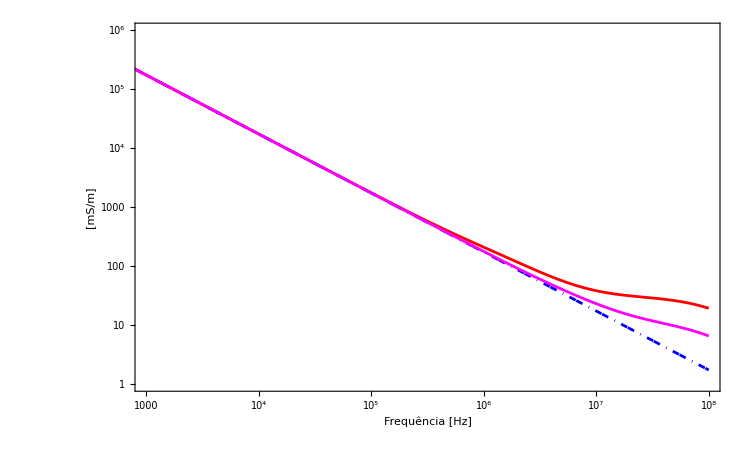

```mathematica
pcable01=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle1,PlotRange->{{1000,10^8},{1,10^6}}];
pcable02=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo2[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle2];
pcable03=ListLogLogPlot[Transpose[{f,1/Abs[Ycabo3[[Range[nf],1,1]]]}], 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"},PlotStyle->plstyle3];
ppp=Show[{pcable01,pcable02,pcable03}]
```

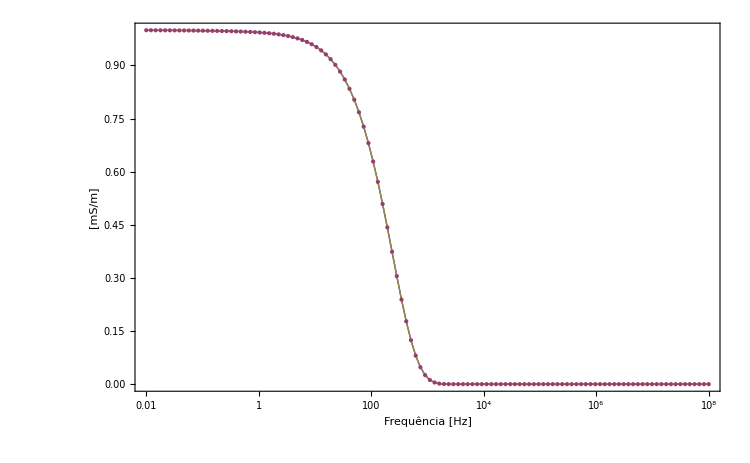

```mathematica
ListLogLinearPlot[{
Transpose@{f,Re[eigAfase[[All,1]] ]},
Transpose@{f,Re[eigAfase2[[All,1]] ]},    
Transpose@{f,Re[eigAfase3[[All,1]] ]}}, 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"}]
```

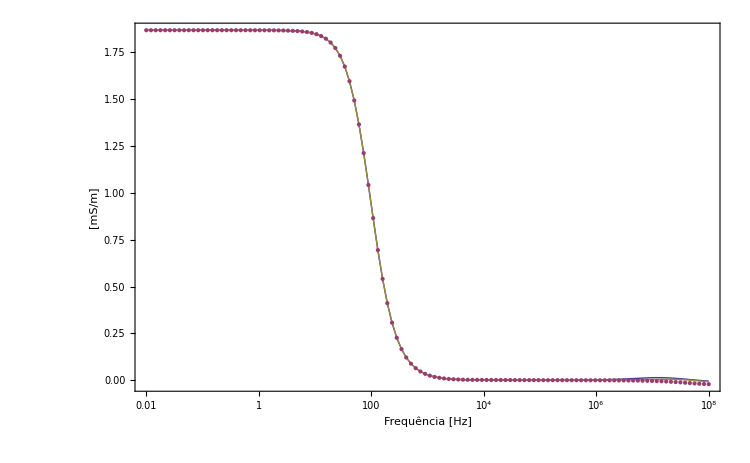

```mathematica
rrr2=ListLogLinearPlot[{
Transpose@{f,Re[Yn[[All,1]] ]},
Transpose@{f,Re[Yn2[[All,1]] ]},
Transpose@{f,Re[Yn3[[All,1]] ]}}, 
Joined->{True,False},
FrameLabel-> {"Frequência [Hz]","[mS/m]"},
BaseStyle->{Medium,FontFamily->"Helvetica"}]
```